```mathematica
RALP1[a_,b_,n_,s_,col_]:=Module[{rt},
rt=RecurrenceTable[{x[i+1]==1-(.2+.01a)*x[i]^2+y[i],
y[i+1]==(0.9991+.0001b)*x[i],x[0]==0.,y[0]==0.},{x,y},{i,1,n}];
ListPlot[rt,ColorFunction->Function[{x,y},ColorData[col][2.5Cos[x+y+.56]^2]],
Axes->False,Background->RGBColor["black"],ImageSize->s,AspectRatio->1]];
{RALP1[0,0,10000,400,"NeonColors"],RALP1[-11,-19987,9000,400,"BrightBands"]}
```

{-Graphics-,-Graphics-}

```mathematica
RALP2[a_,b_,n_,s_,col_]:=Module[{rt},
rt=RecurrenceTable[{x[i+1]==x[i]+(.684+.001a)(x[i]-(x[i])^2+y[i]),
y[i+1]==y[i]+(.684+.001b)(y[i]-(y[i])^2+x[i]),x[0]==.1,y[0]==.01},{x,y},{i,1,n}];
ListPlot[rt,ColorFunction->col,Axes->False,Background->RGBColor["black"],
ImageSize->s,AspectRatio->1]];
{RALP2[0,0,15000,400,"BrightBands"],RALP2[33,-35,20000,400,"NeonColors"]}
```

{-Graphics-,-Graphics-}

```mathematica
RALP3[a_,b_,c_,d_,n_,s_,col_]:=Module[{rt,a1,b1,c1,d1},
a1=.85+.001a;b1=.9+.01b;c1=.4+.01c;d1=9+.1d;
rt=RecurrenceTable[{x[i+1]==
a1+b1(x[i]Cos[c1-d1/(1+x[i]^2+y[i]^2)]-y[i]Sin[c1-d1/(1+x[i]^2+y[i]^2)]),
y[i+1]==b1(x[i]Sin[c1-d1/(1+x[i]^2+y[i]^2)]+y[i]Cos[c1-d1/(1+x[i]^2+y[i]^2)]),
x[0]==.4,y[0]==.5},{x,y},{i,1,n}];
ListPlot[rt,ColorFunction->Function[{x,y},col[Cos[16x+25y]^2]],
Axes->False,Background->RGBColor["black"],ImageSize->s,AspectRatio->1]];
{RALP3[0,0,0,0,25000,400,Hue],RALP3[-72,10,75,-50,15000,400,ColorData["BrightBands"]]}
```

{-Graphics-,-Graphics-}

```mathematica
RALPC[a_,n_,s_,col_]:=Module[{rt},
rt=RecurrenceTable[{x[i+1]==Re[a+(1-a)*(x[i]+I*y[i])],
y[i+1]==Im[a+(1-a)*(x[i]+I*y[i])],
x[0]==Re[(1+2I)*a],y[0]==Im[(1+2I)*a]},{x,y},{i,1,n}];
ListPlot[rt,ColorFunction->col,Axes->False,Background->RGBColor["black"],
ImageSize->s,AspectRatio->1]];
{RALPC[.01+.15I,100000,400,"BrightBands"],RALPC[.05+.21I,100000,400,"NeonColors"]}
```

{-Graphics-,-Graphics-}

```mathematica
CPP[a_,b_,c_,s_]:=ParametricPlot3D[{a*Cos[v]Sinh[u]-b*Cos[c*v]Sinh[c*u],
a*Sin[v]Sinh[u]+b*Sin[c*v]Sinh[c*u],Cos[a*v]Cosh[a*u]},
{u,-1,1},{v,-Pi,Pi},PlotStyle->{RGBColor["steelblue"],Opacity[.2]},
Axes->False,Boxed->False,AspectRatio->1,ViewPoint->{.1,0,2},PlotRange->All,PlotPoints->50,
Mesh->{30,50},MeshStyle->{Magenta,Cyan},ImageSize->s,Background->RGBColor["silver"]];
{CPP[2,.6,3,400],CPP[8,4,3,400]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
CPP2[a_,b_,c_,s_]:=ParametricPlot3D[{u*Cos[a*v],u*Sin[b*v],-v*Cos[c*u]},
{u,-2Pi,2Pi},{v,0,2Pi},PlotStyle->{RGBColor["steelblue"],Opacity[.2]},
Axes->False,Boxed->False,AspectRatio->1,PlotRange->All,ViewPoint->{.8,.8,.9},PlotPoints->50,
Mesh->{25,50},MeshStyle->{RGBColor["crimson"],Cyan},ImageSize->s,Background->RGBColor["silver"]];
{CPP2[1,1,1,400],CPP2[4,-3,1,400]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
MSPP[a_,b_,c_,d_,s_]:=Module[{h,x,y,z},
h=a(1+u^2Sin[v]^2); z=b(Cos[u]+u*Sin[u])Sin[v]/h;
y=b(-u*Cos[u]+Sin[u])Sin[v]/h; x=(Log[Tan[v/c]]/c+Cos[v]/h)/b;
ParametricPlot3D[{x,y,z},{u,-3Pi,3Pi},{v,d,Pi-d},PlotRange->All,
PlotStyle->{RGBColor["steelblue"],Opacity[.1]},Axes->False,Boxed->False,
AspectRatio->1,ViewPoint->{.3,1,0},PlotPoints->50,Mesh->{90,30},
MeshStyle->{White,Cyan},ImageSize->s,Background->RGBColor["silver"]]];
MSPP[1,2,2,.001,600]
```

-Graphics3D-

```mathematica
MSPP2[a_,b_,c_,s_]:=Module[{x,y,z},
x=a(2+Cos[u])Cos[v]^3*Sin[v];
y=b(2+Cos[u+2Pi/3])Cos[v+2Pi/3]^2*Sin[v+2Pi/3]^2; 
z=c(2+Cos[u-2Pi/3])Cos[v+2Pi/3]^2*Sin[v+2Pi/3]^2;
ParametricPlot3D[Table[{i*x,j*y,k*z},{i,{-1,1}},{j,{-1,1}},{k,{-1,1}}],
{u,0,2Pi},{v,0,Pi},AspectRatio->1,PlotRange->All,PlotPoints->20,
PlotStyle->Directive[RGBColor["steelblue"],Opacity[.2]],Axes->False,Boxed->False,
Mesh->{20,20},MeshStyle->{White,Cyan},ImageSize->s,Background->RGBColor["silver"]]];
MSPP2[1,1,1,600]
```

-Graphics3D-

```mathematica
MSPP4[a_,b_,c_,s_]:=Module[{x,y,z},
x=v*Cos[u]-a*v^4Cos[b*u]; y=v*Sin[u]+a*v^4Sin[b*u];z=Exp[c*Log[v]]*Cos[c*u];
ParametricPlot3D[Table[{i*x,j*y,k*z},{i,{-2,2}},{j,{1,2}},{k,{1,2}}],
{u,0,4Pi},{v,0,1},AspectRatio->1,PlotPoints->30,Axes->False,Boxed->False,
PlotStyle->Directive[Cyan,Opacity[.4]],Mesh->{30,15},MeshStyle->{White,Cyan},
ImageSize->s,Background->RGBColor["silver"],ViewPoint->{.1,.4,.9}]];
MSPP4[.5,2,1.5,600]
```

-Graphics3D-

```mathematica
MSPP3[s_]:=Module[{x,y,z},
x=u - u^3/3 + u *v^2; y=v- v^3/3 + v *u^2; z=u^2-v^2;
ParametricPlot3D[Table[{i*x,j*y,k*z},{i,{-2,1}},{j,{-2,1}},{k,{-2,1}}],
{u,-2,2},{v,-2,2},AspectRatio->1,PlotRange->All,PlotPoints->30,
PlotStyle->Directive[Cyan,Opacity[.3]],Axes->False,Boxed->False,
Mesh->{15,25},MeshStyle->{RGBColor["mintcream"],RGBColor["steelblue"]},
ImageSize->s,Background->RGBColor["silver"],ViewPoint->{.1,.1,1.4}]];
MSPP3[600]
```

-Graphics3D-

```mathematica
G1[u,v]:=LaplaceTransform[Sin[x + y],{x,y},{u,v}]
G2[u,v]:=LaplaceTransform[(x*y)^2 E^(-x+y),{x ,y},{u,v}]
{G1[u,v],G2[u,v]}
```

{(4 ⅇ^(-π (u+v)) (u+v) Sinh[π u] Sinh[π v])/((1-ⅇ^(-2 π u)) (1-ⅇ^(-2 π v)) (1+u^2) (1+v^2)),4/((1+u)^3 (-1+v)^3)}

```mathematica
F[u,v]:=LaplaceTransform[Cos[x + y],{x,y},{u,v}]
Plot3D[{Cos[u+v],Evaluate[F[u,v]]},{u,-Pi,Pi},{v,-Pi,Pi},
Axes->False,PlotStyle->Opacity[.7],Mesh->{50,50},MeshStyle->Gray,
ImageSize->500,Boxed->False,AspectRatio->1]
```

-Graphics3D-

```mathematica
RCCP1[s_]:=Module[{a,k,n,t,x0,y0},
k=RandomInteger[{3,6}]; n=RandomInteger[{3,15}]; x0=Random[]; y0=Random[]; a=RandomInteger[{10,170}];t=RandomInteger[{2,4}];
Graphics[{Table[{Hue[2*i/n],Thickness[.1^t],GeometricTransformation[KochCurve[k,{0,a °,-a °,-a °,a °}]/.Line->BSplineCurve,
RotationTransform[i*Pi/n,{.5,0}]]},{i,2n}],Text[{a,k,n},{0,-.7}],Text[{t,x0,y0},{.9,.7}]},
ImageSize->s,Background->RGBColor["silver"]]]
{RCCP1[400],RCCP1[400]}
```

{-Graphics-,-Graphics-}

```mathematica
RFCP1[f_,s_]:=Module[{k,n,t,x0,y0},
k=RandomInteger[{2,5}]; n=RandomInteger[{5,11}]; x0=Random[]; y0=Random[]; t=RandomInteger[{2,4}];
Graphics[Table[{Hue[i/n],Thickness[.1^t], GeometricTransformation[f[k]/.Line->BSplineCurve,
RotationTransform[i*Pi/n,{x0,y0}]]},{i,2n}],ImageSize->s,Background->RGBColor["silver"],
PlotLabel->{k,n,t,x0,y0}]]
{RFCP1[HilbertCurve,400],RFCP1[SierpinskiCurve,400]}
```

{-Graphics-,-Graphics-}

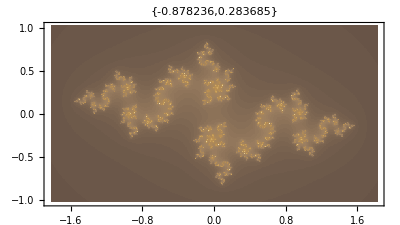
{-Graphics-,-Graphics-}

```mathematica
RJSP1[c_,d_,s_]:=Module[{a,b},a=.1*Random[]; b=.1*Random[];
JuliaSetPlot[c+a +(d+b)*I,ColorFunction->"CoffeeTones",PlotLabel->{c+a,d+b},ImageSize->s]]
{RJSP1[-.9,.2,400],RJSP1[.3,.4,400]}
```

```mathematica
RJSP2[s_,col_]:=Module[{a,n},a=.1*Random[];n=RandomInteger[{10,15}] ;
JuliaSetPlot[z^2/(z^n-.5-a),z,ImageSize->s,ColorFunction->col,PlotLabel->{a,n}]];
{RJSP2[400,"CherryTones"],RJSP2[400,"BrightBands"]}
```

{-Graphics-,-Graphics-}

```mathematica
EmbeddedHTML["<script src='https://d3js.org/d3.v4.min.js'></script><svg id='svg1' style='width:500px; height:500px; background-color:ghostwhite;'><script>var n=640; var m=30; var i,j,k,xmax,xmin; var margin={top:m,right:m,bottom:m,left:m}; var width=500-margin.left-margin.right; var height=500-margin.top-margin.bottom; function get_integer(xmin,xmax) {return Math.floor(Math.random()*(xmax-xmin+1))+xmin;}; function get_color(i) {var r=get_integer(20*i,255); var g=get_integer(20*i,255); var b=get_integer(20*i,255); return '#'+r.toString(16)+g.toString(16)+b.toString(16);} var a=get_integer(7,15),b=get_integer(10,24); function make_data(j) {return d3.range(0,n).map(function(i) {return {'x':4*j*(Math.cos(0.01*i)+Math.cos(a*0.01*i)/2+Math.sin((a+b)*0.01*i)/3),'y':4*j*(Math.sin(0.01*i)+Math.sin(a*0.01*i)/2+Math.cos((a+b)*0.01*i)/3)} }); }; var xScale=d3.scaleLinear().domain([-24,24]).range([0,width+2*m]),yScale=d3.scaleLinear().domain([-24,24]).range([height+2*m,0]); var svg1=d3.select('#svg1').attr('width',width+margin.left+margin.right).attr('height',height+margin.top+margin.bottom).attr('transform','translate('+margin.left+','+margin.top+')'); var line=d3.line().curve(d3.curveMonotoneX).x(function(d) {return xScale(d.x);}).y(function(d) {return yScale(d.y);}); for (k=1; k<4; k++) {var data=make_data(k); svg1.append('path').datum(data).attr('class','line').attr('d',line).attr('fill','none').attr('stroke-width',2).transition().duration(5000).styleTween('stroke',function() {var col1=get_color(k); var col2=get_color(k); return d3.interpolate(col1,col2);}); }; svg1.append('text').attr('transform','translate('+20+','+20+')').style('fill','#aaa').text('a='+a+'; b='+b);</script></svg>",ImageSize->{550,550}]
```

Null<script src='https://d3js.org/d3.v4.…ext('a='+a+'; b='+b);</script></svg><script src='https://d3js.org/d3.v4.min.js'></script><svg id='svg1' style='width:500px; height:500px; background-color:ghostwhite;'><script>var n=640; var m=30; var i,j,k,xmax,xmin; var margin={top:m,right:m,bottom:m,left:m}; var width=500-margin.left-margin.right; var height=500-margin.top-margin.bottom; function get_integer(xmin,xmax) {return Math.floor(Math.random()*(xmax-xmin+1))+xmin;}; function get_color(i) {var r=get_integer(20*i,255); var g=get_integer(20*i,255); var b=get_integer(20*i,255); return '#'+r.toString(16)+g.toString(16)+b.toString(16);} var a=get_integer(7,15),b=get_integer(10,24); function make_data(j) {return d3.range(0,n).map(function(i) {return {'x':4*j*(Math.cos(0.01*i)+Math.cos(a*0.01*i)/2+Math.sin((a+b)*0.01*i)/3),'y':4*j*(Math.sin(0.01*i)+Math.sin(a*0.01*i)/2+Math.cos((a+b)*0.01*i)/3)} }); }; var xScale=d3.scaleLinear().domain([-24,24]).range([0,width+2*m]),yScale=d3.scaleLinear().domain([-24,24]).range([height+2*m,0]); var svg1=d3.select('#svg1').attr('width',width+margin.left+margin.right).attr('height',height+margin.top+margin.bottom).attr('transform','translate('+margin.left+','+margin.top+')'); var line=d3.line().curve(d3.curveMonotoneX).x(function(d) {return xScale(d.x);}).y(function(d) {return yScale(d.y);}); for (k=1; k<4; k++) {var data=make_data(k); svg1.append('path').datum(data).attr('class','line').attr('d',line).attr('fill','none').attr('stroke-width',2).transition().duration(5000).styleTween('stroke',function() {var col1=get_color(k); var col2=get_color(k); return d3.interpolate(col1,col2);}); }; svg1.append('text').attr('transform','translate('+20+','+20+')').style('fill','#aaa').text('a='+a+'; b='+b);</script></svg>

```mathematica
EmbeddedHTML["<script src='https://code.highcharts.com/highcharts.js'></script><div id='container2' style='height:600px; width:600px; margin:0 auto'><script>function getinteger(min,max) {return Math.floor(Math.random()*(max-min+1))+min;}; function ar(k,a,b) {return Array(640).fill(k).map((k,t)=>[k*(Math.cos(0.01*t)+Math.cos(a*0.01*t)/2+Math.sin((a+b)*0.01*t)/3),k*(Math.sin(0.01*t)+Math.sin(a*0.01*t)/2+Math.cos((a+b)*0.01*t)/3)]);}; function col(i) {var r=getinteger(i,255); var g=getinteger(i,255); var b=getinteger(i,255);    return 'rgb('+r.toString()+','+g.toString()+','+b.toString()+')';}; var series=[]; var i; var n=12; var a=getinteger(7,15); var b=getinteger(10,24); for (i=1; i<n+1; i++) {series.push({name:i.toString(),color:col(i),lineWidth:1,data:ar(i,a,b)})}; Highcharts.chart('container2', {chart:{type:'line',backgroundColor:'mintcream'},xAxis:{title:{text:'x'}},yAxis:{title:{text:'y'}},title:{text:'Random Parametric Plot: a,b = '+[a,b].toString()},credits:{enabled:false},legend:{enabled:false},series:series});</script></div>"
,ImageSize->{650,650}]
```

Null<script src='https://code.highcharts…lse},series:series});</script></div><script src='https://code.highcharts.com/highcharts.js'></script><div id='container2' style='height:600px; width:600px; margin:0 auto'><script>function getinteger(min,max) {return Math.floor(Math.random()*(max-min+1))+min;}; function ar(k,a,b) {return Array(640).fill(k).map((k,t)=>[k*(Math.cos(0.01*t)+Math.cos(a*0.01*t)/2+Math.sin((a+b)*0.01*t)/3),k*(Math.sin(0.01*t)+Math.sin(a*0.01*t)/2+Math.cos((a+b)*0.01*t)/3)]);}; function col(i) {var r=getinteger(i,255); var g=getinteger(i,255); var b=getinteger(i,255);    return 'rgb('+r.toString()+','+g.toString()+','+b.toString()+')';}; var series=[]; var i; var n=12; var a=getinteger(7,15); var b=getinteger(10,24); for (i=1; i<n+1; i++) {series.push({name:i.toString(),color:col(i),lineWidth:1,data:ar(i,a,b)})}; Highcharts.chart('container2', {chart:{type:'line',backgroundColor:'mintcream'},xAxis:{title:{text:'x'}},yAxis:{title:{text:'y'}},title:{text:'Random Parametric Plot: a,b = '+[a,b].toString()},credits:{enabled:false},legend:{enabled:false},series:series});</script></div>